```mathematica
AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]];
If[!MemberQ[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]],AppendTo[$Path,FileNameJoin[{$HomeDirectory,"GDC","DialecticalStructures"}]]];
Print["Package path ",FindFile["GDCComparisons`"]];
Print["Package path ",FindFile["GDCAnalysis3`"]];
<<GDCAnalysis3`
<<GDCComparisons`
```

Package path /home/carla/GDC/DialecticalStructures/GDCComparisons.m

Package path /home/carla/GDC/DialecticalStructures/GDCAnalysis3.m

```mathematica
filesAR=FileNames["/home/carla/GDC/CH_Pool/MUR/GDC_CHP_AR_MUR_ALL_Out/*.txt"];
inputAR=Map[Get[#]&, filesAR];
dojAR=inputAR[[All,1]];
zAR=inputAR[[All,2]];
fAR=inputAR[[All,3]];
filesBR=FileNames["/home/carla/GDC/CH_Pool/MUR/GDC_CHP_BR_MUR_ALL_Out/*.txt"];
inputBR=Map[Get[#]&, filesBR];
dojBR=inputBR[[All,1]];
zBR=inputBR[[All,2]];
fBR=inputBR[[All,3]];
```

```mathematica
(*MIN Values*)
Map[dojBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[zBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
Map[fBR[[#]][[1]][["value"]]&,Range[Length[fBR]]]
```

{0.,0.,0.,0.,0.,0.,0.}

{-1,-1,-1,-1,-1,-1,-1}

{-1,-1,-1,-1,-1,-1,-1}

```mathematica
tsAR={1,2,3,4,5,6,7,8};
tsBR={1.5,2.5,3.5,4.5,5.5,6.5,7.5};
tsAll=Union[tsAR,tsBR];
```

```mathematica
dojMax=maxValFunc[tsAR, tsBR, dojAR, dojBR, "MUR", "DOJ"]
zMax=maxValFunc[tsAR, tsBR, zAR, zBR, "MUR", "Z"]
fMax=maxValFunc[tsAR, tsBR, fAR, fBR, "MUR", "F"]
```

{{1,0.0137255},{1.5,0.0137255},{2,0.0137255},{2.5,0.00923483},{3,0.0625},{3.5,0.0625},{4,0.0625},{4.5,0.0930233},{5,0.00884956},{5.5,0.00487805},{6,0.0232558},{6.5,0.0232558},{7,1.},{7.5,1.},{8,1.}}

{{1,0.0120331},{1.5,0.0120885},{2,0.0120885},{2.5,0.00765387},{3,0.0622655},{3.5,0.0622745},{4,0.0622745},{4.5,0.0927096},{5,0.00868509},{5.5,0.00480805},{6,0.0232031},{6.5,0.0232037},{7,1.},{7.5,1.},{8,1.}}

{{1,0.780469},{1.5,0.790282},{2,0.790282},{2.5,0.712905},{3,0.992525},{3.5,0.99281},{4,0.99281},{4.5,0.993278},{5,0.963509},{5.5,0.971706},{6,0.995474},{6.5,0.995527},{7,1},{7.5,1},{8,1}}

```mathematica
dojTat=Get["/home/carla/GDC/CONF/MUR/MUR_DOJ.txt"]
zTat=Get["/home/carla/GDC/CONF/MUR/MUR_Z.txt"]
fTat=Get["/home/carla/GDC/CONF/MUR/MUR_F.txt"]
```

{{1,0.00196078},{1.5,0.00196078},{2,0.00196078},{2.5,0.00131926},{3,0.0625},{3.5,0.0625},{4,0.0625},{4.5,0.0232558},{5,0.00884956},{5.5,0.00487805},{6,0.0232558},{6.5,0.0232558},{7,1.},{7.5,1.},{8,1.}}

{{1,0.0017165},{1.5,0.00173069},{2,0.00173069},{2.5,0.0010979},{3,0.0622655},{3.5,0.0622745},{4,0.0622745},{4.5,0.0231234},{5,0.00850675},{5.5,0.00458898},{6,0.0232031},{6.5,0.0232037},{7,1.},{7.5,1.},{8,1.}}

{{1,0.778431},{1.5,0.789956},{2,0.789956},{2.5,0.712634},{3,0.992525},{3.5,0.99281},{4,0.99281},{4.5,0.988676},{5,0.925416},{5.5,0.888114},{6,0.995474},{6.5,0.995527},{7,1},{7.5,1},{8,1}}

```mathematica
(*dojPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "MUR"},PlotStyle->{Red, Blue},PlotLabel->"DOJ : CH=MAX vs. CH=MUR geg EV&BK=MUR",PlotMarkers->{{"X",12}, {"M",12}}, ImageSize->400];
zPlot=ListLogPlot[{dojMax,dojTat},PlotLegends->{"MAX", "MUR"},PlotStyle->{Red, Blue},PlotLabel->"Z : CH-MAX vs. CH_MUR geg EV&BK=MUR",PlotMarkers->{{"X",12}, {"M",12}}, ImageSize->400];
fPlot=ListLogPlot[{fMax,fTat},PlotLegends->{"MAX", "MUR"},PlotStyle->{Red, Blue},PlotLabel->"F : CH-MAX vs. CH_MUR geg EV&BK=MUR",PlotMarkers->{{"X",12}, {"M",12}}, ImageSize->400];
confMAX=Column[{dojPlot,zPlot,fPlot}]*)
```

```mathematica
(* dojBR[[5,2]][["value"]]
dojTat[[10]]
dojBR[[5,2]][["list"]][[1;;3]]
Map[compCHMaxFunc[First[persMixFunc["MUR"]], #, tatCH , dojBR]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["MUR"]],# , tatCH, "CH", "PEN"]&,{4.5}]
Map[vvPosFunc[First[persMixFunc["MUR"]],# , dojBR,  "CH", "PEN"]&,{4.5}]*)
```

```mathematica
tatCH=Map[Get[#]&,FileNames["/home/carla/GDC/POS/*.txt"]];
persInd=First[persMixFunc["MUR"]]
pers="MUR";
```

7

```mathematica
(*VV-Value von CH-TAT : Ähnlichkeit von CH-TAT mit DEV*)
Map[{#,vvPosFunc[persInd,# , tatCH, "CH", "PEN"]}&,{1,2,3,4,5,6,7,8}]
```

{{1,0.733333},{2,0.733333},{3,0.666667},{4,0.666667},{5,0.733333},{6,0.8},{7,1.},{8,1.}}

```mathematica
(*Veritistic Value von CH-MAX : Ähnlichkeit von CH_MAX mit DEV*)
dojVV=vvCHMaxFunc[tsAR, tsBR, dojAR, dojBR,pers];
zVV=vvCHMaxFunc[tsAR, tsBR, zAR, zBR,pers];
fVV=vvCHMaxFunc[tsAR, tsBR, fAR, fBR,pers];
dojVVHist=vvHistPointsFunc[dojVV];
zVVHist=vvHistPointsFunc[zVV];
fVVHist=vvHistPointsFunc[fVV];
```

15

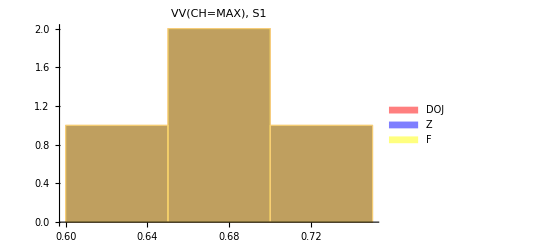
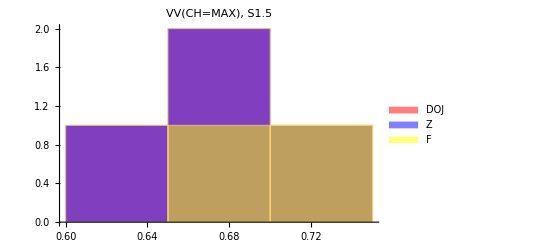
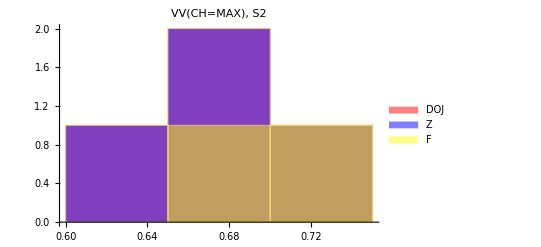
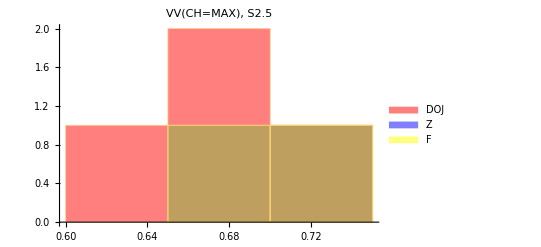
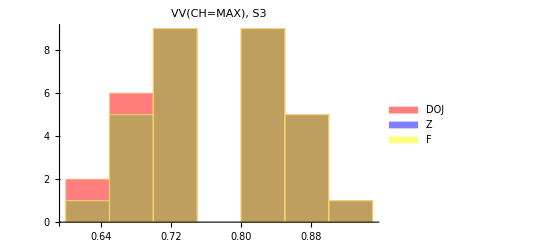
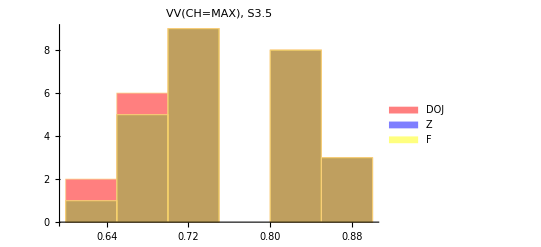
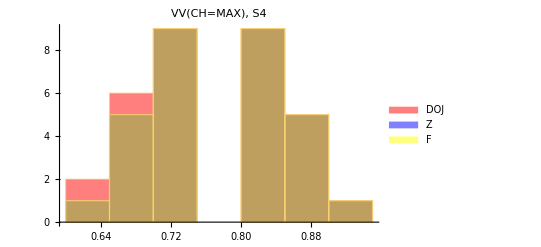
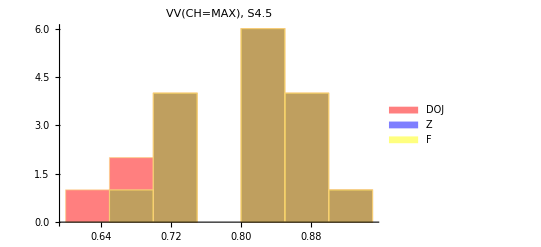
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
(*ListPlot[dojVVHist,PlotLegends->{"DOJ"},PlotStyle->{Red},PlotLabel->"VV CH=MAX geg EV&BK=MUR",PlotMarkers->{{"D",12}}, PlotRange->{0,1.05}]
ListPlot[zVVHist, PlotLegends->{"Z"},PlotStyle->{Blue},PlotLabel->"VV CH=MAX geg EV&BK=MUR",PlotMarkers->{{"Z",12}}, PlotRange->{0,1.05}]
ListPlot[fVVHist, PlotLegends->{"F"},PlotStyle->{Green},PlotLabel->"VV CH=MAX geg EV&BK=MUR",PlotMarkers->{{"F",12}}, PlotRange->{0,1.05}]
vvMaxPlot=ListPlot[{dojVVHist,zVVHist,fVVHist}, PlotLegends->{"DOJ","Z","F"},PlotStyle->{Red,Blue,Green},PlotLabel->"VV CH=MAX geg EV&BK=MUR",PlotMarkers->{{"D",12},{"Z",12},{"F",12}}, PlotRange->{0,1.05}]*)
timL={1,1.5,2,2.5,3,3.5,4,4.5,5,5.5,6,6.5,7,7.5,8};
Length[timL]
hist=Map[Histogram[{dojVV[[#,2]],zVV[[#,2]],fVV[[#,2]]}, PlotLabel->"VV(CH=MAX),    S"<>ToString[timL[[#]]],ImageSize->400, ChartLegends->{"DOJ","Z","F"},ChartStyle->{Red,Blue,Yellow}]&,Range[Length[timL]]];
histOut=Grid[{hist[[1;;3]],hist[[4;;6]],hist[[7;;9]],hist[[10;;12]],hist[[13;;15]]},ItemSize->35]
```

```mathematica
SetDirectory["/home/carla/GDC/CH_Pool/MUR/"];
(*Export["COMP_DOJ_CHTAT_CHMAX_MUR.jpeg",dojPlot,ImageResolution->300]
Export["COMP_CHTAT_CHMAX_MUR.jpeg",confMAX,ImageResolution->300]*)
Export["VV_CHMAX_HIST_MUR.jpeg",histOut,ImageResolution->300]
Put[dojVVHist, "gdc_DOJ_VV_CHMAX_MUR.txt"]
Put[zVVHist, "gdc_Z_VV_CHMAX_MUR.txt"]
Put[fVVHist, "gdc_F_VV_CHMAX_MUR.txt"]
```

VV_CHMAX_HIST_MUR.jpeg